Set Parameter

```mathematica
k=1
A=1
l=0.1
```

1

1

0.1

Set Matrix K

```mathematica
K={{(k*A)/l,(-k*A)/l,0,0,0,0,0,0,0,0,0},{(-k*A)/l,(2k*A)/l,(-k*A)/l,0,0,0,0,0,0,0,0},{0,(-k*A)/l,(2k*A)/l,(-k*A)/l,0,0,0,0,0,0,0},{0,0,(-k*A)/l,(2k*A)/l,(-k*A)/l,0,0,0,0,0,0},{0,0,0,(-k*A)/l,(2k*A)/l,(-k*A)/l,0,0,0,0,0},{0,0,0,0,(-k*A)/l,(2k*A)/l,(-k*A)/l,0,0,0,0},{0,0,0,0,0,(-k*A)/l,(2k*A)/l,(-k*A)/l,0,0,0},{0,0,0,0,0,0,(-k*A)/l,(2k*A)/l,(-k*A)/l,0,0},{0,0,0,0,0,0,0,(-k*A)/l,(2k*A)/l,(-k*A)/l,0},{0,0,0,0,0,0,0,0,(-k*A)/l,(2k*A)/l,(-k*A)/l},{0,0,0,0,0,0,0,0,0,(-k*A)/l,(k*A)/l}}
```

{{10.,-10.,0,0,0,0,0,0,0,0,0},{-10.,20.,-10.,0,0,0,0,0,0,0,0},{0,-10.,20.,-10.,0,0,0,0,0,0,0},{0,0,-10.,20.,-10.,0,0,0,0,0,0},{0,0,0,-10.,20.,-10.,0,0,0,0,0},{0,0,0,0,-10.,20.,-10.,0,0,0,0},{0,0,0,0,0,-10.,20.,-10.,0,0,0},{0,0,0,0,0,0,-10.,20.,-10.,0,0},{0,0,0,0,0,0,0,-10.,20.,-10.,0},{0,0,0,0,0,0,0,0,-10.,20.,-10.},{0,0,0,0,0,0,0,0,0,-10.,10.}}

Apply boundary condition and Solve Unknow

```mathematica
Solve[Dot[K,{0,Subscript[T, 2],Subscript[T, 3],Subscript[T, 4],Subscript[T, 5],Subscript[T, 6],Subscript[T, 7],Subscript[T, 8],Subscript[T, 9],Subscript[T, 10],0}]==A*l*{0,0,0,0,0+0.4,0.4+0.5,0.5+0.6,0.6+0.7,0.7+0.8,0.8,0}+{Subscript[Q, 1],0,0,2.5,0,0,0,0,0,0,Subscript[Q, 11]}]//N
```

{{Q_1→-1.94,Q_11→-1.16,T_2→0.194,T_3→0.388,T_4→0.582,T_5→0.526,T_6→0.466,T_7→0.397,T_8→0.317,T_9→0.224,T_10→0.116}}

Find Exact Solution

```mathematica
s[x_]:=2x *(HeavisideTheta[x-0.4]-HeavisideTheta[x-0.8])
DSolve[{D[k*T'[x],x]+2.5*DiracDelta[x-0.3]+s[x]==0,T[0]==0,T[1]==0},T[x],x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T[x]→0.333333 (5.794 x+1.024 HeavisideTheta[-0.8+x]-1.92 x HeavisideTheta[-0.8+x]+1. x^3 HeavisideTheta[-0.8+x]-0.128 HeavisideTheta[-0.4+x]+0.48 x HeavisideTheta[-0.4+x]-1. x^3 HeavisideTheta[-0.4+x]+2.25 HeavisideTheta[-0.3+x]-7.5 x HeavisideTheta[-0.3+x])}}

Cheack

```mathematica
1/3 (0.4-0.4^3)
```

0.112

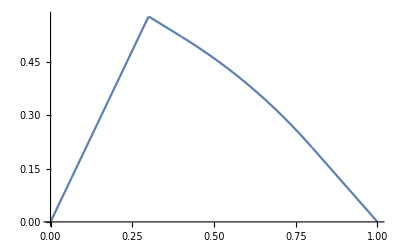

```mathematica
Plot[0.3333333333333333 (5.794 x+1.0240000000000005 HeavisideTheta[-0.8+x]-1.9200000000000004 x HeavisideTheta[-0.8+x]+1. x^3 HeavisideTheta[-0.8+x]-0.12800000000000006 HeavisideTheta[-0.4+x]+0.4800000000000001 x HeavisideTheta[-0.4+x]-1. x^3 HeavisideTheta[-0.4+x]+2.25 HeavisideTheta[-0.3+x]-7.5 x HeavisideTheta[-0.3+x]),{x,0,1},PlotRange->All]
```